# Zhou-Fan Model (SIR):(Sections 5 and 6 in the manuscript)

```mathematica
ClearAll["Global‘*"]
SetDirectory[NotebookDirectory[]];
<<Epid.wl;<<mods.wl;(*<<"def.m";(*trG*)*)

(*The Format commands bridge between Mathematica and Latex notations *)
Format[γr]:=Subscript[γ,r];Format[dr]:=Subscript[d,r];
Format[μi]:=Subscript[μ,i];

(*Numerical conditions: Param is close to the numerical condition used in ZF for codimension 2 bifurcation maps;cN is used for simulations*)
Param=Thread[{Λ,δ,γ,β,ξ,μ}->{16,2/10,12/100,1/100,1/1000,12/100}];
ParNum=Thread[{ω,α,η}->{7/64,179/64,α/ω}];
Print["Numerical condition cN used for simulations"]
cN=Join[ParNum,Param]

(*Numerical conditions: ParamGc corresponding to the one given by Gupta, they are used in the checking of his computations*)
paramGc=Thread[{Λ,δ,γ,β,ξ,μ}->{1/2,2/10,1/10,2/10,7/100,1/10}]; 

(*Conditions on g[i],T[i] for setting  the model, simplifying notations (μi),important constants (sd), relations between parametrizations, (ηH,ωH) are the coordinates of H when the two endemic points and DFE collide in the map *)

cZF={g[i]->β i/(1+ξ i),T[i]->i η ω/(ω+i),μi->μ+δ}; ceta={η->α/ω};
 sd=Λ/μ;ηH=sd β-(γ+μ+δ) ;ωH=(μ (β Λ-μ (γ+δ+μ)))/(β Λ (β+μ ξ));

(*inputting the model defined in mods*)
mod=SIRgT;S=mod[[4]];
Vg=mod[[5]];
RHS=mod[[1]]; RHSclosed=RHS//.cZF//FullSimplify; 
Print[" (s'
i'
r')= ", RHSclosed//MatrixForm]
```

Numerical condition cN used for simulations

{ω→7/64,α→179/64,η→α/ω,Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25}

(s'
i'
r')= (Λ-s μ-(i s β)/(1+i ξ)
i (-γ-δ-μ+(s β)/(1+i ξ)-(η ω)/(i+ω))
-r μ+i (γ+(η ω)/(i+ω)))

### Two dim case of ZF:

```mathematica
(*Setting of the 2dim- model, computation of R0, jac, det, tr, and FPs*)
var={s,i};RHS2=Drop[RHSclosed,-1]; pars=Par[RHS2,var];cpZ=Thread[Drop[Variables[RHSclosed],3]>0];
Print["Two dim ZF model is ", RHS2//MatrixForm]

(*Computation of R0 using the script*)
SIRF={RHS2,var,pars};
mode=SIRF;inf={2};
cdfe=DFE[mode,inf]//FullSimplify//Flatten;
dfe=var/.Thread[var[[inf]]->0]/.cdfe//FullSimplify;
ngm=NGM[mode,inf];
K=ngm[[6]];
Print[ "DFE =", dfe, ", and  R0=", R0=Eigenvalues[K][[1]]/.cdfe] 
b0=β/.Solve[R0==1,β][[1]]//FullSimplify(*critical β used in the diagram of Bif*);

jac2=Grad[RHS2,var];det2=Det[jac2];tr2=Tr[jac2];
Print["Two-dim Jacobian is ",jac2//FullSimplify//MatrixForm]

eqF2=Thread[Flatten[RHS2==0]];
 equi2=Solve[eqF2,{s,i}];
 Print[" Two endemic fixed points !"]
FPn=equi2//.cN ;FPn//N
 RHS2E={RHS2[[1]],Simplify[RHS2[[2]]/i]};

(*Section 5 in the paper*)
Print[" detG factors"]
Timing[detG=GroebnerBasis[{RHS2[[1]],RHS2[[2]]/i,det2},pars,var][[1]]//FullSimplify]
(*Timing[trG=GroebnerBasis[{s1,ifac,tr},Params,X][[1]]](*32 secs, long*)(*Do not simplify*)
Save["def.m",trG]*)
```

Two dim ZF model is (Λ-s μ-(i s β)/(1+i ξ)
i (-γ-δ-μ+(s β)/(1+i ξ)-(η ω)/(i+ω)))

DFE ={Λ/μ,0}, and  R0=(β Λ)/(μ (γ+δ+η+μ))

Two-dim Jacobian is (-μ-(i β)/(1+i ξ) | -(s β)/(1+i ξ)^2
(i β)/(1+i ξ) | -γ-δ-μ+(s β)/(1+i ξ)^2-(η ω^2)/(i+ω)^2)

Two endemic fixed points !

{{s→133.333,i→0.},{s→86.1361,i→6.61878},{s→69.9589,i→10.99}}

detG factors

{7.84375,(β Λ-μ (γ+δ+η+μ)) (μ^2 (γ+δ+μ-(γ+δ+η+μ) ξ ω)^2+β^2 (Λ^2+2 Λ (γ+δ-η+μ) ω+(γ+δ+η+μ)^2 ω^2)+2 β μ (-Λ (γ+δ+μ)-(γ+δ+μ) (γ+δ+η+μ) ω+Λ (γ+δ-η+μ) ξ ω+(γ+δ+η+μ)^2 ξ ω^2))}

```mathematica
(*Elimination of s via plugging, chP, dis, checking examples for Hopf*)

Print["s formula cs from first and sec eqs of RHS2 are"]
cs=Flatten[Solve[RHS2[[1]]==0,s]]
cs2=Flatten[Solve[(RHS2[[2]]/i)==0,s]]
se02=s/.cs2;

(*Equation for endemic i using the chP and FPs equations *)
poli=Collect[Factor[Numerator[Together[RHS2[[2]]/.cs]]]/(-i),i];
Print["sec. order A i^2 + B i + C=0 for endemic i is"]
pol2= Collect[ poli//FullSimplify,i]

Print["coeffs are"]
cf=CoefficientList[poli,i];
Aa=cf[[3]];Bb=cf[[2]]; Cc=cf[[1]];
Print["{A,B,C} =",{Aa,Bb,Cc}//FullSimplify]

ie=Solve[poli==0,i](*endemic i*);
Print["Trace of jac2 in terms of i after substitution of solution of cs2 is "]
tri=tr2/.cs2//FullSimplify
nutr=Factor[Numerator[tri]];
rest=Resultant[poli,nutr,i](*it will be used in the numerical illustrations*);
tra2=tri/.ie[[2]](*Trace at the second endemic point*);
Print["dis "]
dis=Discriminant[poli,i]//FullSimplify

(*Computation of the coordinates corresponding to the HOpf point in the two dimensional map*)
Print[" Example of Hopf pnt in the case of one endemic point (Tr[E2]=0 , dis>0, R0>1, Bb<0)"]
bnd23=Join[FindInstance[Join[{dis>0&&tra2==0 &&Bb<0&&R0>1},Thread[Drop[Variables[RHS2],2]>0],{η==α/ω}]//.Param,
{ω,α,η}][[1]],Param];
%//N
Chop[Eigenvalues[jac2/.cs2/.ie[[2]]/.Param/.bnd23]//N]
```

s formula cs from first and sec eqs of RHS2 are

{s→(Λ (1+i ξ))/(i β+μ+i μ ξ)}

{s→((1+i ξ) (γ+δ+μ+(η ω)/(i+ω)))/β}

sec. order A i^2 + B i + C=0 for endemic i is

i^2 (γ+δ+μ) (β+μ ξ)-β Λ ω+μ (γ+δ+η+μ) ω+i (-β Λ+μ (γ+δ+μ)+(γ+δ+η+μ) (β+μ ξ) ω)

coeffs are

{A,B,C} ={(γ+δ+μ) (β+μ ξ),-β Λ+μ (γ+δ+μ)+(γ+δ+η+μ) (β+μ ξ) ω,(-β Λ+μ (γ+δ+η+μ)) ω}

Trace of jac2 in terms of i after substitution of solution of cs2 is

-μ-(i β)/(1+i ξ)+(i η ω)/(i+ω)^2-(i ξ (γ+δ+μ+(η ω)/(i+ω)))/(1+i ξ)

dis

μ^2 (γ+δ+μ-(γ+δ+η+μ) ξ ω)^2+β^2 (Λ^2+2 Λ (γ+δ-η+μ) ω+(γ+δ+η+μ)^2 ω^2)+2 β μ (-Λ (γ+δ+μ)-(γ+δ+μ) (γ+δ+η+μ) ω+Λ (γ+δ-η+μ) ξ ω+(γ+δ+η+μ)^2 ξ ω^2)

Example of Hopf pnt in the case of one endemic point (Tr[E2]=0 , dis>0, R0>1, Bb<0)

{ω→6.,α→5.00625,η→0.834376,Λ→16.,δ→0.2,γ→0.12,β→0.01,ξ→0.001,μ→0.12}

{0.+0.15125 ⅈ,0.-0.15125 ⅈ}

### Computation of some important points in the codim 2 map:

```mathematica
Print["The point HP from the Map"]

HP=Solve[Join[{η==ηH&&Bb==0},cpZ,{η==α/ω}]//.Param,{ω,α,η}][[1]]//FullSimplify;
HP//N
Print["Check of Eigenvalues at H "]
Eigenvalues[jac2/.equi2[[2]]/.Param/.HP]//N


eq=Flatten[Join[{dis==0&&tra2==0},cpZ]]//.Join[{η->α/ω},Param];
Print["BTP Symb is", BTP=Solve[eq,{ω,α},Reals][[1]]//FullSimplify," =",BTP//N]

Print["This is BogdanovTP"]
eq=Join[BTP,Param,{η->α/ω}]
cS=NSolve[(RHS2//.eq)==0,var,WorkingPrecision->60];
Print["Check of Det at the BTP at E2 "]
Chop[N[det2//.Join[eq,cS[[2]]],60]]
(*w of BT*)
wBT=ω/.BTP;
η0=sd β-(μ+γ+δ)(*it comes from Solve[R0==1,η]*);
Print["Two B pts?"]
BP=Solve[Join[{η==η0&&tra2==0&&dis>0},cpZ,{η==α/ω}]//.Param,{ω,α,η},
Reals]//FullSimplify;
BP//N
(*Save["def.m",BTP];Save["def.m",BP]*)
```

The point HP from the Map

{ω→7.94466,α→7.09723,η→0.893333}

Check of Eigenvalues at H

{-0.12,0.}

BTP Symb is{ω→Root6.84Root[-36408000000000+1969099000000 #1+431356651000 #1^2+8566772533 #1^3&,3]6.841829512107803,α→(100 (4960+Root-3.88 × 10^3Root[-166963297160-58095840 #1+#1^3&,2]-3877.10865259884))/17457} ={ω→6.84183,α→6.20319}

This is BogdanovTP

{ω→Root6.84Root[-36408000000000+1969099000000 #1+431356651000 #1^2+8566772533 #1^3&,3]6.841829512107803,α→(100 (4960+Root-3.88 × 10^3Root[-166963297160-58095840 #1+#1^3&,2]-3877.10865259884))/17457,Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25,η→α/ω}

Check of Det at the BTP at E2

0

Two B pts?

{{ω→5.15735,α→4.60724,η→0.893333},{ω→7.35966,α→6.57463,η→0.893333}}

```mathematica
(*Numeric approach, using Param*)
test[RI]=Join[FindInstance[Join[{dis>0,R0<1,(tra2)>0, Bb<0,ω>2},cpZ,{η==α/ω}]//.Param,
{ω,α,η}][[1]],Param];
test[II]=Join[FindInstance[Join[{dis>0,R0>1,(tra2)>0},cpZ,{η==α/ω}]//.Param,
{ω,α,η}][[1]],Param];
test[III]=Join[FindInstance[Join[{dis>0,R0>1,(tra2)<0},cpZ,{η==α/ω}]//.Param,
{ω,α,η}][[1]],Param];
test[IV]=Join[FindInstance[Join[{dis>0&&R0<1&&Bb>0,ω<11},cpZ,{η==α/ω}]//.Param,
{ω,α,η}][[1]],Param];
test[V]=Join[FindInstance[Join[{dis<0,R0<1},cpZ,{η==α/ω}]//.Param,{ω,α,η}][[1]]
,Param];
test[VI]=Join[FindInstance[Join[{dis>0,R0<1,(tra2)<0},cpZ,{η==α/ω}]//.Param,
{ω,α,η}][[1]],Param];
test[VIa]=Join[FindInstance[Join[{dis>0,R0<1,(tra2)<0},cpZ,{η==α/ω}]//.Param,
{ω,α,η},3][[2]],Param];

testBoIIandIII=Join[FindInstance[Join[{dis>0&&tra2==0 &&Bb<0&&R0>1},cpZ,{η==α/ω}]//.Param,
{ω,α,η}][[1]],Param];
testBoIandVI=Join[FindInstance[Join[{dis>0 &&Bb<0&&tra2==0&&R0<1,ω<wBT},cpZ,{η==α/ω}]//.Param,
{ω,α,η}][[1]],Param];
testBoIandVII=Join[FindInstance[Join[{dis>0 &&Bb<0&&tra2==0&&R0<1,ω>wBT},cpZ,{η==α/ω}]//.Param,
{ω,α,η}][[1]],Param];
testBoIIandI=Join[FindInstance[Join[{dis>0&&tra2>0 &&Bb<0&&R0==1},cpZ,{η==α/ω}]//.Param,
{ω,α,η}][[1]],Param];
testBoIIandIV=Join[FindInstance[Join[{dis>0 &&Bb>0&&R0==1},cpZ,{η==α/ω}]//.Param,
{ω,α,η}][[1]],Param];
testBoIandVIa=Join[FindInstance[Join[{tra2==0&& dis>0 && R0<1},cpZ,{η==α/ω}]//.Param,
{ω,α,η},6][[6]],Param];

testHP=Join[HP,Param];
testBTP=Join[BTP,Param];
testBP=Join[BP[[1]],Param]

Print["between I and II at R0=1 downward B1"]
testR1=Join[Param,Thread[{ω,α}->{901/195,60367/14625}]]
testR2=Join[Param,Thread[{ω,α}->(({ω,α}//.BP[[1]])+({ω,α}//.BP[[2]]))/2]]
testR3=Join[Param,Thread[{ω,α}->(({ω,α}//.HP)+({ω,α}//.BP[[2]]))/2]]
testR4=Join[Param,Thread[{ω,α}->{8139/1028,181771/25700}]]



(*Now on Gupta parameters*)

testGca=Join[paramGc,Thread[{ω,α}->{10/99, 9/99}]];
testGcb=Join[paramGc,Thread[{ω,α}->{10000/103387, 9000/103387}]];
testGcc=Join[paramGc,Thread[{ω,α}->{10/108, 9/108}]];
testGcd=Join[paramGc,Thread[{ω,α}->{1/11, 9/110}]];
testGc4=Join[paramGc,Thread[{ω,α}->{1000000000/1604038240, 900000000/1604038240}]];
testG3a=Join[paramGc,Thread[{ω,α}->{100000000/1063265757, 90000000/1063265757}]];


R0TD={R0-1, tra2, dis, Bb};
Print["R0-1, Tr,Dis, B for region I is "]
R0TD//.Join[test[RI],ceta]//N
Print["R0-1, Tr,Dis, B for the boundary betωeen II and III is "]
Chop[Evaluate[R0TD//.Join[testBoIIandIII,ceta]//N]]
Print["R0-1, Tr,Dis, B of Gupta (Fig 1a) is : "]
R0TD//.Join[testGca,ceta]//N
Print["R0-1, Tr,Dis, B of Gupta (Fig 1b) is : "]
R0TD//.Join[testGcb,ceta]//N
Print["R0-1, Tr,Dis, B of Gupta (Fig 1c) is : "]
R0TD//.Join[testGcc,ceta]//N
Print["R0-1, Tr,Dis, B of Gupta (Fig 1d) is : "]
R0TD//.Join[testGcd,ceta]//N
Print["R0-1, Tr,Dis, B, of Gupta (Fig 3a) is : "]
R0TD//.Join[testG3a,ceta]//N

Print["at H, dis is"]
dis//.testHP//FullSimplify

Print["tra2 at H when μ=1/12 is "]
tra2//.testHP//N
```

{ω→Root5.16Root[-14273010000000+5043092010000 #1-486916463000 #1^2+8858269519 #1^3&,1]5.157354044656745,α→(67 Root7.14 × 10^5Root[-4270613049090000000+10903443990000 #1-7607000 #1^2+#1^3&,1]713731.3835940915)/10379325,η→67/75,Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25}

between I and II at R0=1 downward B1

{Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25,ω→901/195,α→60367/14625}

{Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25,ω→1/2 (Root5.16Root[-14273010000000+5043092010000 #1-486916463000 #1^2+8858269519 #1^3&,1]5.157354044656745+Root7.36Root[-14273010000000+5043092010000 #1-486916463000 #1^2+8858269519 #1^3&,2]7.359657040257573),α→1/2 ((67 Root7.14 × 10^5Root[-4270613049090000000+10903443990000 #1-7607000 #1^2+#1^3&,1]713731.3835940915)/10379325+(67 Root1.02 × 10^6Root[-4270613049090000000+10903443990000 #1-7607000 #1^2+#1^3&,2]1.0185102974582857e6)/10379325)}

{Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25,ω→1/2 (2010/253+Root7.36Root[-14273010000000+5043092010000 #1-486916463000 #1^2+8858269519 #1^3&,2]7.359657040257573),α→1/2 (8978/1265+(67 Root1.02 × 10^6Root[-4270613049090000000+10903443990000 #1-7607000 #1^2+#1^3&,2]1.0185102974582857e6)/10379325)}

{Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25,ω→8139/1028,α→181771/25700}

R0-1, Tr,Dis, B for region I is

{-0.349179,0.0139738,0.000608759,-0.0624949}

R0-1, Tr,Dis, B for the boundary betωeen II and III is

{0.046264,0,0.0016453,-0.0298199}

R0-1, Tr,Dis, B of Gupta (Fig 1a) is :

{-0.230769,0.024036,0.0000733967,-0.0328182}

R0-1, Tr,Dis, B of Gupta (Fig 1b) is :

{-0.230769,0.0000111711,0.000193019,-0.0339716}

R0-1, Tr,Dis, B of Gupta (Fig 1c) is :

{-0.230769,-0.0183133,0.00031084,-0.0350833}

R0-1, Tr,Dis, B of Gupta (Fig 1d) is :

{-0.230769,-0.025093,0.00035956,-0.0355364}

R0-1, Tr,Dis, B, of Gupta (Fig 3a) is :

{-0.230769,-0.0121655,0.000268999,-0.0346912}

at H, dis is

0

tra2 at H when μ=1/12 is

-0.12

#### Bifurcation Map:

{Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25}

dis at BTP is

0

Dis at H =

0.

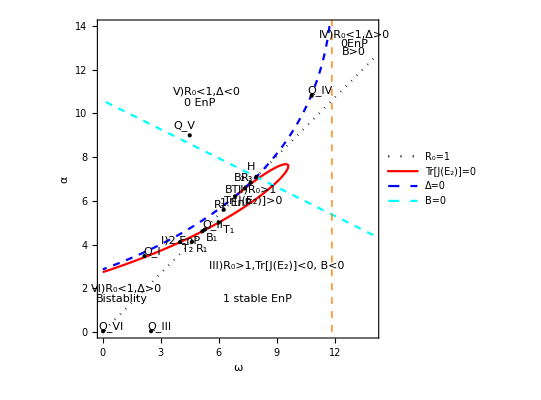

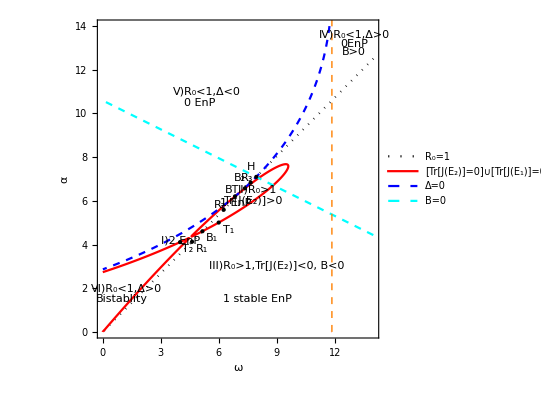

fig6ns.pdf

fig62.pdf

```mathematica
(**Fig 6ns/3, Fig62/4 *)
cn=Param
xm=0;ym=0;xM=14;yM=14;
(*μ/(Subscript[v, 1])//.cn//N*)
p1g=Graphics[{Thick,Orange,Dashed,Line[{{μ/((β+ μ ξ))//.cn,0},{μ/((β+ μ ξ))//.cn,45}}]}];
R0ωa=(R0//.cn/.η->α/ω);
disωa=(dis/.ceta//.cn);
Bbωa=(Bb/.ceta//.cn);
trωa=(tra2/.ceta//.cn);
trω2=((rest)/.ceta//.cn);

(*trω=((trG//.cv1)/.ceta//.cn);*)
ptr=ContourPlot[trωa==0,{ω,xm,xM},{α,ym,yM},ContourStyle->{Red},PlotPoints -> 200,  
 AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},PlotLegends->{"Tr[J(E_2)]=0"}];
  ptr2=ContourPlot[trω2==0,{ω,xm,xM},{α,ym,yM},PlotPoints -> 290, 
 MaxRecursion -> 2, WorkingPrecision -> 35, ContourStyle->{Red},
 AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},PlotLegends->{"[Tr[J(E_2)]=0]∪[Tr[J(E_1)]=0]"}];
 
 
Print["dis at BTP is "]
Chop[Evaluate[disωa//.testBTP//N]]
Print["Dis at H ="]
dis//.testHP//N

pR0=ContourPlot[R0ωa==1,{ω,xm,xM},{α,ym,yM},ContourStyle->{Black,Dotted},
 AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},Frame->True,PlotLegends->{"R_0=1"}];
 
pD=ContourPlot[disωa==0,{ω,xm,xM},{α,ym,yM},
ContourStyle->{ Blue,Dashed}, AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},
PlotLegends->{"Δ=0"}];

pB=ContourPlot[Bbωa==0,{ω,xm,xM},{α,ym,yM},
ContourStyle->{Dashed,Cyan}, AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},PlotLegends->{"B=0"}];

 epi= {Black,Style[Text["V)R_0<1,Δ<0",{5.4,11}],13],Style[Text["0 EnP",{5,10.5}],13],
Style[Text["Tr[J(E_2)]>0",{7.8,6}],6],Style[Text["II)R_0>1",{8,6.5}],7],Style
[Text["1 EnP",{6.9,5.9}],6],
Style[Text["IV)R_0<1,Δ>0",{13,13.6}],10],Style[Text["0EnP",{13,13.2}],12],
Style[Text["B>0",{13,12.8}],12],
Style[Text[" VI)R_0<1,Δ>0",{1.2,2}],10],Style[Text["Bistablity",{1,1.5}],10],
Style[Text[" I)2 EnP",{4,4.2}],7],
Style[Text[" III)R_0>1,Tr[J(E_2)]<0, B<0",{9,3}],13],
Style[Text["1 stable EnP",{8,1.5}],13]};

PH=Text["H",Offset[{-5,10},{ω,η ω}//.testHP]];PHp={PointSize[Medium],Style[Point[{ω,η ω}
//.testHP],Yellow]};
PBT=Text["BT",Offset[{-3,6},{ω,α}//.testBTP//N]];PBTp={PointSize[Medium],Style[Point[
{ω,α}//.testBTP//N],Red]};
BP1=Text["B_1",Offset[{10,-7},{ω,α}//.BP[[1]]]];BP1p={PointSize[Medium],Style[Point[
{ω,α}//.BP[[1]]],Green]};
BP2=Text["B_2",Offset[{-5,10},{ω,α}//.BP[[2]]]];BP2p={PointSize[Medium],Style[Point[
{ω,α}//.BP[[2]]],Blue]};
P1=Text["R_1",Offset[{10,-7},{ω,α}//.testR1//N]];P1p={PointSize[Medium],Style[Point[
{ω,α}//.testR1//N],Purple]};
(*P4=Text["R_4",Offset[{10,-7},{ω,α}//.testR4]];P4p={PointSize[Medium],
Style[Point[{ω,α}//.testR4],Purple]};*)



P3=Text["R_3",Offset[{-4,5},({ω,α}//.testR3//N)]];
P3p={PointSize[Medium],Style[Point[{ω,α}//.testR3//N],Purple]};
P2=Text["R_2",Offset[{-4,5},{ω,α}//.testR2//N]];
P2p={PointSize[Medium],Style[Point[{ω,α}//.testR2//N],Purple]};
QI=Text["Q_I",Offset[{8,5},{ω,α}//.test[RI]]];QIp={PointSize[Medium],Style[Point[
{ω,α}//.test[RI]],Magenta]};
QII=Text["Q_II",Offset[{8,5},{ω,α}//.test[II]]];QIIp={PointSize[Medium],Style[Point[
{ω,α}//.test[II]],Magenta]};
QIII=Text["Q_III",Offset[{8,5},{ω,α}//.test[III]]];QIIIp={PointSize[Medium],Style[Point[
{ω,α}//.test[III]],Magenta]};
QIV=Text["Q_IV",Offset[{8,5},{ω,α}//.test[IV]]];QIVp={PointSize[Medium],Style[Point[
{ω,α}//.test[IV]],Magenta]};
QV=Text["Q_V",Offset[{-5,10},{ω,α}//.test[V]]];QVp={PointSize[Medium],Style[Point[
{ω,α}//.test[V]],Magenta]};
QVI=Text["Q_VI",Offset[{8,5},{ω,α}//.test[VI]]];QVIp={PointSize[Medium],
Style[Point[{ω,α}//.test[VI]],Magenta]};
QVIa=Text["Q_VIa",Offset[{8,5},{ω,α}//.test[VIa]]];QVIap={PointSize[Medium],
Style[Point[{ω,α}//.test[VIa]],Magenta]};
T1=Text["T_1",Offset[{10,-7},{ω,α}//.testBoIIandIII]];T1a={PointSize[Medium],
Style[Point[{ω,α}//.testBoIIandIII],Black]};
T2=Text["T_2",Offset[{8,-7},{ω,α}//.testBoIandVIa]];T2a={PointSize[Medium],
Style[Point[{ω,α}//.testBoIandVIa],Black]};
regions={RI,II,III,IV,V,VI};
pt=Table[{ω,α}//.test[j],{j,regions}];
pG=Table[Text[P[j],Offset[{-5,10},pt[[j]]]],{j,6}];

epiP={PH,PHp,PBT,PBTp,BP1,BP1p,BP2,BP2p,P1,P1p,P3,P3p,P2,P2p,(*P4,P4p,*)QI,QIp,QII,
QIIp,QIII,QIIIp,QIV,QIVp,QV,QVp,QVI,QVIp,T1,T1a,T2,T2a}//N;
epiP1={PH,PHp,PBT,PBTp,BP1,BP1p,BP2,BP2p,P1,P1p,P3,P3p,P2,P2p,T1,T1a,T2,T2a}//N;
fig6F=Show[{pR0,ptr,pD,pB,p1g},PlotStyle->Join[ColorData[97,"ColorList"]],Filling->{3->{0,Yellow}}
,Epilog->{epi,epiP},FrameLabel->{ω,"α"},
PlotRange->{{xm,xM},{ym,yM}}]
fig62=Show[{pR0,ptr2,pD,pB,p1g},PlotStyle->Join[ColorData[97,"ColorList"]],Filling->{3->{0,Yellow}}
,Epilog->{epi,epiP1},FrameLabel->{ω,"α"},
PlotRange->{{xm,xM},{ym,yM}}]

Export["fig6ns.pdf",fig6F]
Export["fig62.pdf",fig62]
```

#### Blow-up of the Map:

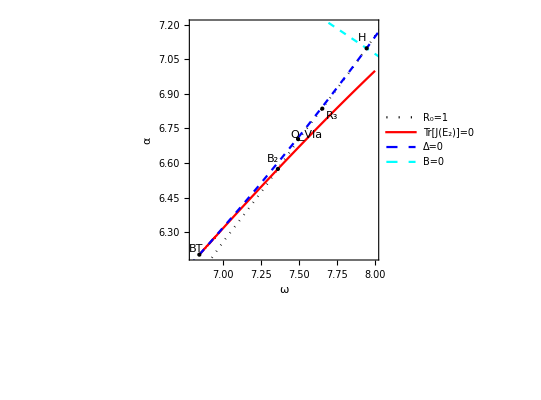

fig6BT.pdf

```mathematica
(*xm=6.8;ym=6.25;xM=7.8;yM=6.9;*)
xm=6.8;ym=6.2;xM=8;yM=7.2;
trωa=((tra2)/.ceta//.cn);
ptr=ContourPlot[trωa==0,{ω,xm,xM},{α,ym,yM},ContourStyle->{Red},PlotPoints -> 200,
 AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},PlotLegends->{"Tr[J(E_2)]=0"}];
 P3=Text["R_3",Offset[{10,-7},{ω,α}//.testR3//N]];
 P3p={PointSize[Medium],Style[Point[{ω,α}//.testR3//N],Purple]};
 epiP1={PH,PHp,PBT,PBTp,BP1,BP1p,BP2,BP2p,P1,P1p,P3,P3p,QVIa,QVIap}//N;
fig6F=Show[{pR0,ptr,pD,pB,p1g},PlotStyle->Join[ColorData[97,"ColorList"]],Filling->{3->{0,Yellow}}
,Epilog->{epiP1},FrameLabel->{ω,"α"},
PlotRange->{{xm,xM},{ym,yM}}]
Export["fig6BT.pdf",fig6F]
```

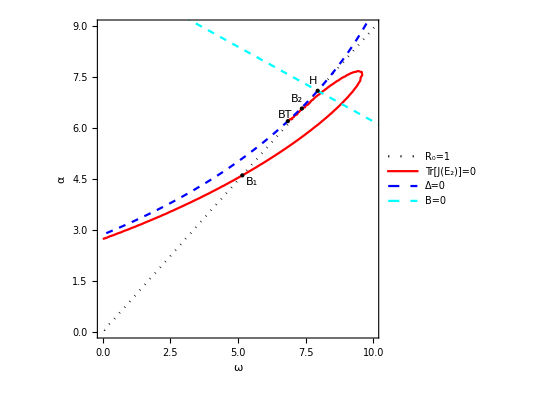

fig6n.pdf

```mathematica
(*xm=6.8;ym=6.25;xM=7.8;yM=6.9;*)
xm=0;ym=0;xM=10;yM=9;
epiP={PH,PHp,PBT,PBTp,BP1,BP1p,BP2,BP2p}//N;
trωa=((tra2)/.ceta//.cn);
ptr=ContourPlot[trωa==0,{ω,xm,xM},{α,ym,yM},ContourStyle->{Red},
 AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},PlotLegends->{"Tr[J(E_2)]=0"}];
 
fig6F=Show[{pR0,ptr,pD,pB,p1g},PlotStyle->Join[ColorData[97,"ColorList"]],Filling->{3->{0,Yellow}}
,Epilog->{epiP},FrameLabel->{ω,"α"},
PlotRange->{{xm,xM},{ym,yM}}]
Export["fig6n.pdf",fig6F]
```

#### Bifurcation diagram :

{ω→1/64,α→1/32,η→2,Λ→16,δ→1/5,γ→3/25,ξ→1/1000,μ→3/25}

β*=0.0183 ,β_(1*)=0.00302031 ,β_(2*)=0.00361597

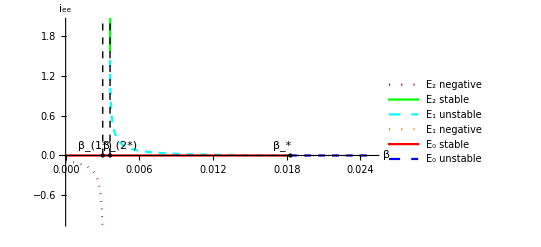

bifZF.pdf

```mathematica
(**Bifurcation Diagram of Region VI*)
cn=Drop[test[VI],{7}]
xm=0;ym=-1;xM=0.025;yM=2;

dis0=β/.Solve[dis==0,β];

Print["β*=",b0n= b0/.η->α/ω//.cn//N, " ,β_(1*)=", bc1=dis0[[1]]/.η->α/ω//.cn//N, " ,β_(2*)=", bc2=dis0[[2]]/.η->α/ω//.cn//N]

lin1=Line[{{ bc1,0},{ bc1,yM}}];
li1=Graphics[{Thick,Black,Dashed,lin1}];
lin2=Line[{{ bc2,0},{ bc2,yM}}];
li2=Graphics[{Thick,Black,Dashed,lin2}];
pE2a=Plot[{i/.ie[[2]]/.η->α/ω}//.cn,{β,0,bc1},PlotStyle->{Dotted,Thick,Purple},PlotRange->All,PlotLegends->{"E_2 negative"}];
pE2b=Plot[{i/.ie[[2]]/.η->α/ω}//.cn,{β,bc1,xM},PlotStyle->{Thick,Green},
PlotRange->All,PlotLegends->{"E_2 stable"}];
pE1a=Plot[{i/.ie[[1]]/.η->α/ω}//.cn,{β,0,b0n},PlotStyle->{Dashed,Thick,Cyan},PlotRange->All,PlotLegends->{"E_1 unstable"}];
pE1b=Plot[{i/.ie[[1]]/.η->α/ω}//.cn,{β,b0n,xM},PlotStyle->{Dotted,Thick,Orange},
PlotRange->All,PlotLegends->{"E_1 negative"}];
pdfea=Plot[0,{β,0, b0n},PlotStyle->{Thick,Red},PlotRange->All,
PlotLegends->{"E_0 stable"}];
pdfeb=Plot[0,{β,b0n, xM},PlotStyle->{Dashed,Thick,Blue},PlotRange->All,
PlotLegends->{"E_0 unstable"}];
bifZF=Show[{pE2a, pE2b,pE1a, pE1b,pdfea,pdfeb,li1,li2},PlotRange->{{xm,xM},{ym,yM}},Epilog->
{{Text["β_*",Offset[{-8,10},{ b0n,0}]],{PointSize[Large],
Style[Point[{ b0n,0}],Orange]},Text["β_(2*)",Offset[{10,10},{ bc2,0}]],
{PointSize[Large],Style[Point[{ bc2,0}],Yellow]},Text["β_(1*)",Offset[{-8,10},{ bc1,0}]],
{PointSize[Large],Style[Point[{ bc1,0}],Black]}}
},AxesLabel->{"β","i_ee"}]

Export["bifZF.pdf",bifZF]
```

## Symbolic Analysis of the model:

```mathematica
Print["RHS of general gT model SIRgT is RHS=",RHS//MatrixForm, " and RHS of closed version RHSclosed  is ",
RHSclosed//FullSimplify//MatrixForm]
Print["Check the sum of RHS ",Total[RHSclosed]//FullSimplify]

nu=NullSpace[S];di=nu//Length;
V=Sum[x[j] nu[[j]],{j,di}];
cx={x[1]->r μ,x[2]->i μi,x[3]->s μ};
Vp=V/.cx;
Print["null space of ",S//MatrixForm," is",
V//MatrixForm," and in terms of pars Vp",Vp//MatrixForm];
V={v1,v2,v3,s μ,i μi,r μ};
so=Solve[S.V==0][[1]];
Print["null space of S  in terms of pars ",so]
```

RHS of general gT model SIRgT is RHS=(Λ-s μ-s g[i]
-i γ-i μ_i+s g[i]-T[i]
i γ-r μ+T[i]) and RHS of closed version RHSclosed  is (Λ-s μ-(i s β)/(1+i ξ)
i (-γ-δ-μ+(s β)/(1+i ξ)-(η ω)/(i+ω))
-r μ+i (γ+(η ω)/(i+ω)))

Check the sum of RHS -i δ+Λ-(i+r+s) μ

null space of (1 | -1 | 0 | -1 | 0 | 0
0 | 1 | -1 | 0 | -1 | 0
0 | 0 | 1 | 0 | 0 | -1) is(x[1]+x[2]+x[3]
x[1]+x[2]
x[1]
x[3]
x[2]
x[1]) and in terms of pars Vp(r μ+s μ+i μ_i
r μ+i μ_i
r μ
s μ
i μ_i
r μ)

null space of S  in terms of pars {v1→r μ+s μ+i μ_i,v2→r μ+i μ_i,v3→r μ}

#### Symbolic 3dim model:

```mathematica
(*computation of a Hopf example for the symbolic 3dim  model*)
var={s,i,r};jac=Grad[RHS,var];det=Det[jac];
Print["Jacobian is ",jac//MatrixForm]
chp=-CharacteristicPolynomial[jac,ϵ];
cof=CoefficientList[chp,ϵ]//FullSimplify;
{co0,co1,co2,co3}=cof;

Print["CharacteristicPolynomial has last cof= ",co3//FullSimplify, "  det ",co0," and the other cofs have pars  "]
parc=Variables[cof]
cp=Thread[parc>0];

Heq={co1>0,co1*co2-co0==0,RHS[[3]]==0,RHS[[2]]==0,RHS[[1]]==0};
(*added flux equations*)
cond=Union[Heq,cp,{i>0}];
Print["Example satisfies Hopf Condition under cond: "]
Print["fiH=",fiH=FindInstance[cond,Join[parc,{i,r,Λ,T[i]}]][[1]]]
Print["Check RHS=0 under fiH ",RHS/.fiH]
jaf=jac/.fiH;
Print[" Eigenvalues of",jaf//MatrixForm," are ",Eigenvalues[jaf]//N]
Tr[jac]/.fiH
```

Jacobian is (-μ-g[i] | -s g'[i] | 0
g[i] | -γ-μ_i+s g'[i]-T'[i] | 0
0 | γ+T'[i] | -μ)

CharacteristicPolynomial has last cof= 1  det μ (g[i] (γ+μ_i+T'[i])+μ (γ+μ_i-s g'[i]+T'[i])) and the other cofs have pars

{s,γ,μ,μ_i,g[i],g'[i],T'[i]}

Example satisfies Hopf Condition under cond:

fiH={s→8,γ→1/2,μ→1,μ_i→1,g[i]→1,g'[i]→1,T'[i]→9/2,i→1,r→7,Λ→16,T[i]→13/2}

Check RHS=0 under fiH {0,0,0}

Eigenvalues of(-2 | -8 | 0
1 | 2 | 0
0 | 5 | -1) are {0.+2. ⅈ,0.-2. ⅈ,-1.}

-1